# POKEMON GAN

This is inspired by Jérôme Louradour, Wolfram Research. For details, please check https://blog.wolfram.com/2020/08/18/generative-adversarial-networks-gans-in-the-wolfram-language/ .

```mathematica
pokemons=ImageResize[ImagePad[#,,RGBColor[1,1,1]],{64,64}]&/@DeleteMissing@EntityValue[EntityList@"Pokemon",EntityProperty["Pokemon","Image"]];
```

```mathematica
RandomSample[pokemons,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
generator=NetChain[{LinearLayer["Input"->100],NetTake[NetModel["CycleGAN Horse-to-Zebra Translation Trained on ImageNet Competition Data"],{10,All}],ResizeLayer[{224,224}]},"Output"->NetDecoder["Image"]]
```

```mathematica
discriminator=NetChain[{NetModel["EfficientNet Trained on ImageNet"],AggregationLayer[Max,1]}]
```

NetChain[<>]

```mathematica
gan=NetGANOperator[{generator,discriminator},"JensenShannon"];
```

```mathematica
ganAsGraph=NetGraph[<|"Generator"->NetReplacePart[generator,LearningRateMultipliers->-1],"Discriminator"->NetInsertSharedArrays[discriminator],
"FooledDiscriminator"->NetInsertSharedArrays[discriminator],"LossReal"->ElementwiseLayer[Function[-Log[#]]],"LossFake"->ElementwiseLayer[Function[-Log[1-#]]]|>,
{NetPort["Sample"]->"Discriminator"->"LossReal"->NetPort["LossReal"],NetPort["Latent"]->"Generator"->"FooledDiscriminator"->"LossFake"->NetPort["LossFake"],"Generator"->NetPort["GeneratedFake"]}]
```

NetGraph[<>]

```mathematica
deconvolutionBlock[numhiddens_,size_]:=NetChain[{DeconvolutionLayer[numhiddens,{5,5},"Stride"->{2,2},PaddingSize->1],PartLayer[{All,1;;size,1;;size}],BatchNormalizationLayer[],Ramp}]
generator=NetChain[{
NetChain[{{512,4,4},BatchNormalizationLayer[],Ramp}],
deconvolutionBlock[256,8],
deconvolutionBlock[128,16],
deconvolutionBlock[64,32],DeconvolutionLayer[3,{5,5},"Stride"->{2,2},PaddingSize->1,"Weights"->0],PartLayer[{All,1;;64,1;;64}],ElementwiseLayer[Tanh[#]*0.5+.5&]},
"Input"->32,
"Output"->NetDecoder["Image"]]
```

NetChain[<>]

```mathematica
convolutionBlock[numhiddens_,size_]:=NetChain[{ConvolutionLayer[numhiddens,{5,5},"Stride"->{2,2},PaddingSize->2],BatchNormalizationLayer[],ElementwiseLayer[Max[#1,0.2 #1]&]}]
discriminator=NetChain[{
ElementwiseLayer[-1+2*#&],
convolutionBlock[64,32],
convolutionBlock[128,16],
convolutionBlock[256,8],
convolutionBlock[512,4],LinearLayer[{},"Weights"->0,"Biases"->None],
LogisticSigmoid},
"Input"->NetEncoder[{"Image",{64,64},"RGB"}]]
```

NetChain[<>]

```mathematica
autoencoder=NetChain[<|
"compressor"->NetTake[discriminator,{All,5}],"latent"->NetChain[{LinearLayer[32],BatchNormalizationLayer[]}],"generator"->generator|>];
```

```mathematica
autoencoderTrainer = NetGraph[<|"autoencoder"->autoencoder,"MSE" -> MeanSquaredLossLayer[]|>,{{"autoencoder",NetPort["Input"]}->"MSE"}];
```

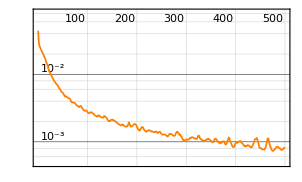
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:16500  rounds:500  time:8.6min  examples/s:1025
data | ,,  training examples:1050  processed examples:528000  skipped examples:0
method | ,,  ADAMoptimizer  batch size32GPU
round | ,,  loss:8.31×10^-4
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
autoEncoderTrainResults=NetTrain[autoencoderTrainer,pokemons,All,TargetDevice->{"GPU",{1,2,3,4}},MaxTrainingRounds->500,BatchSize->32]
trained=autoEncoderTrainResults["TrainedNet"];
```

```mathematica
generator=NetReplacePart[autoencoder[["generator"]],"Output"->NetDecoder["Image"]];
```

```mathematica
discriminator=NetAppend[autoencoder[["compressor"]],LinearLayer[{},"Weights"->0,"Biases"->None],"Input"->NetEncoder[{"Image",{64,64}}]];
```

```mathematica
NetGANOperator[{generator,discriminator}]
```

```mathematica
datagen=Function[<|"Sample"->RandomSample[pokemons,#BatchSize],"Latent"->getRandomLatent[#BatchSize]|>];
getRandomLatent [batchSize_]:=RandomReal[1, {batchSize, 32}]
```

```mathematica
squash=NetGraph[{ElementwiseLayer[#1^2&],AggregationLayer[Total,1],ElementwiseLayer[(√#1)/(1+#1)&],ReplicateLayer[Automatic],ThreadingLayer[Times]},{NetPort["Input"]->1->2->3->4->5,NetPort["Input"]->5},"Input"->{Automatic}];
getRandomLatent [batchSize_]:= squash@ RandomVariate[NormalDistribution[], {batchSize, 32}]
```

```mathematica
frames={};
```

```mathematica
monitor=With[{latents=getRandomLatent[25]},Function[generator,AppendTo[frames,ImageCollage[generator[latents],ImagePadding->1]]]];
```

```mathematica
trainedGan=NetTrain[NetGANOperator[{generator,discriminator}],datagen,TrainingUpdateSchedule->{"Discriminator"->3,"Generator"->3},BatchSize->64,MaxTrainingRounds->50000,TargetDevice->{"GPU",{1,2,3,4}},TrainingProgressReporting->{monitor[NetExtract[#Net,"Generator"]]&,"Interval"->Quantity[250, "Rounds"]}];
```

```mathematica
generator=trainedGan[["Generator"]]
```

```mathematica
newPokemons=generator[getRandomLatent[112]];

ImageAssemble[Partition[SortBy[newPokemons,DominantColors[#,1,Masking->Binarize[ColorDistance[#1,White],0.1]]&],8],Spacings->10,ImageSize->Full]
```